```mathematica
Experiment of college physics 3
Lihong Ao
2019271014
SZU,physics
```

```mathematica
RC串联电路的电感测量
```

```mathematica
(ω L)^2+(Subscript[R, 0]+Subscript[R, L])^2=(Subscript[U, 0]/Subscript[i, max])^2
Subscript[i, max]=Subscript[U, Rmax]/Subscript[R, 0]
L=1/ω √((Subscript[U, 0]/Subscript[U, Rmax] Subscript[R, 0])^2-(Subscript[R, 0]+Subscript[R, L])^2)
```

```mathematica
Subscript[R, 0]=100Ω;Subscript[R, L]=145.63Ω;
```

{{0.17107,0.169639,0.170117,0.172495,0.168201,0.170117,0.171478},{0.162144,0.162144,0.162144,0.162778,0.163412,0.161722,0.162325},{0.163659,0.163659,0.163659,0.162607,0.163659,0.164363,0.163358},{0.165497,0.164958,0.164421,0.164689,0.165497,0.164779,0.164268},{0.170222,0.169617,0.169416,0.169316,0.169496,0.170222,0.170222}}

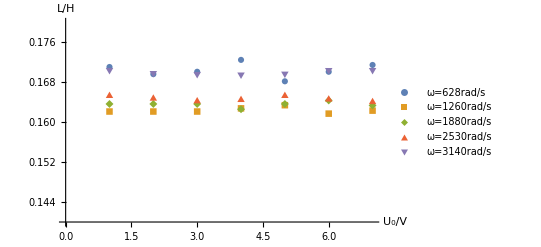

0.16621

0.0000113336

0.0460068

```mathematica
Subscript[U, Rmax]={{0.373,0.747,1.12,1.49,1.87,2.24,2.61},{0.313,0.626,0.939,1.25,1.56,1.88,2.19},{0.254,0.508,0.762,1.02,1.27,1.52,1.78},{0.206,0.413,0.621,0.827,1.03,1.24,1.45},{0.17,0.341,0.512,0.683,0.853,1.02,1.19}};
ω={628,1260,1880,2530,3140};
Subscript[U, 0]=Table[u,{u,1,Length@(Subscript[U, Rmax][[1]])}];
Subscript[R, 0]=100;Subscript[R, L]=145.63;
Subscript[L, ref]=158.9*10^-3;
tabL=Table[√(((Subscript[U, 0][[j]])/(Subscript[U, Rmax][[i]][[j]])Subscript[R, 0])^2-(Subscript[R, 0]+Subscript[R, L])^2)/ω[[i]],{i,1,Length@Subscript[U, Rmax]},{j,1,Length@(Subscript[U, Rmax][[1]])}]
ListPlot[Table[Transpose@{Subscript[U, 0],tabL[[i]]},{i,1,5}],ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"U_0/V","L/H"},PlotRange->{0.14,0.18},PlotLegends->{"ω=628rad/s","ω=1260rad/s","ω=1880rad/s","ω=2530rad/s","ω=3140rad/s"}]
tabLF=Flatten@tabL;
Subscript[L, aver]=Total@tabLF/Length@tabLF      (*均值*)
Subscript[L, var]=Total[Table[(tabLF[[i]]-Subscript[L, aver])^2,{i,1,Length@tabLF}]]/Length@tabLF       (*方差*)
ϵ=Abs[Subscript[L, aver]-Subscript[L, ref]]/Subscript[L, ref]
```

```mathematica
tabLω=Table[Total@tabL[[i]]/Length@(Subscript[U, Rmax][[1]]),{i,1,Length@Subscript[U, Rmax]}]
Total[Table[(tabLω[[i]]-Subscript[L, aver])^2,{i,1,Length@tabLω}]]/Length@tabLω
Table[Total[Table[(tabL[[i]][[j]]-Subscript[L, aver])^2,{j,1,Length@(tabL[[i]])}]]/Length@(tabL[[i]]),{i,1,Length@tabL}]
```

{0.170445,0.162381,0.163566,0.164872,0.169787}

0.0000108348

{0.000019585,0.0000149252,7.22548×10^-6,1.98993×10^-6,0.0000129423}

```mathematica
Subscript[L, aver]=(∑_i Subscript[L, i])/n=0.16621(H),Subscript[L, var]=(∑_i (Subscript[L, i]-Subscript[L, aver])^2)/n=0.0000113(H^2),ϵ=(|Subscript[L, aver]-Subscript[L, ref]|)/Subscript[L, ref]=0.046
```

```mathematica
弹簧振动周期与负载和劲度系数的关系
```

```mathematica
F=-k x
Subscript[m, 0]=ρ Subscript[x, 0]
m x^(..)+∫_0^1 (ρ Subscript[x, 0])/x α x^(..)ⅆα+k x=0
T=2π √((m+Subscript[m, 0]/3)/k)⟹ m=k/(4 π^2)T^2-Subscript[m, 0]/3 ⟹ Log T=Log(2π √(m+Subscript[m, 0]/3))-(Log k)/2
```

```mathematica
Subscript[k, tot]=Subscript[k, 2a]+Subscript[k, 2b]   T=2π/ω    m=1506.2g    Subscript[k, na](n∈{1,2,3,4,5}) 506.2+100i(i∈ℤ:0≤i≤13)
```

```mathematica
T∝m^(1/2),T∝k^(-1/2)
```

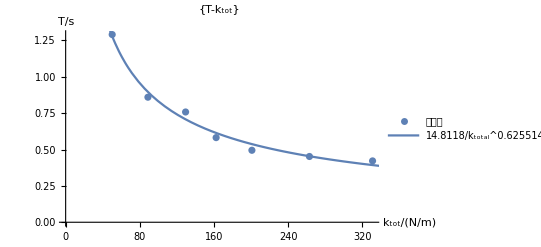

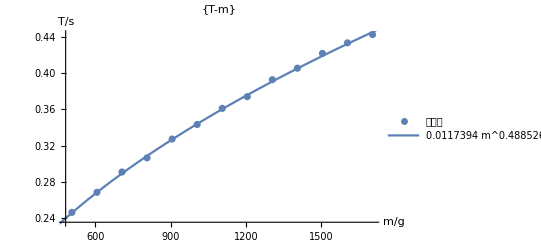

R_1^2→0.992234

R_2^2→0.999576

```mathematica
Clear[ka,kb,tabω,tabT,tabT2,tabm,a,b,c,d,Subscript]
ka=Evaluate@Table[Subscript[k, i,a],{i,1,5}]={25.44529262,163.9344262,63.29113924,99.00990099,24.75247525};
kb=Evaluate@Table[Subscript[k, i,b],{i,1,5}]={24.37013941,167.0870113,66.06977462,101.8797532,24.28544741};
tabω={4.87,7.31,8.29,10.8,12.7,13.9,14.9};
tabω2={25.5,23.4,21.6,20.5,19.2,18.3,17.4,16.8,16,15.5,14.9,14.5,14.2};
tabT=(2π)/tabω;
tabT2=(2π)/tabω2;
tabm=Table[506+100i,{i,0,12}];
Subscript[k, tot]={ka[[1]]+ka[[5]],ka[[1]]+ka[[3]],ka[[3]]+kb[[3]],ka[[3]]+ka[[4]],ka[[4]]+kb[[4]],ka[[2]]+ka[[4]],ka[[2]]+kb[[2]]};
sol1=NMinimize[Total@Table[(tabT[[i]]-a Subscript[k, tot][[i]]^b)^4,{i,1,Length@tabT}],{a,b},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];b=b/.sol1[[2]];
sol2=NMinimize[Total@Table[(tabT2[[i]]-c tabm[[i]]^d)^4,{i,1,Length@tabT2}],{c,d},Method->"SimulatedAnnealing"];
c=c/.sol2[[2]];d=d/.sol2[[2]];
Show[ListPlot[Transpose@{Subscript[k, tot],tabT},AxesLabel->{"k_tot/(N/m)","T/s"},PlotLabel->{T-"k_tot"},ImageSize->400,PlotLegends->{实验值}],Plot[a k^b,{k,0,350},PlotLegends->{a Subscript[k, total]^b}]]
Show[ListPlot[Transpose@{tabm,tabT2},AxesLabel->{"m/g","T/s"},PlotLabel->{T-m},ImageSize->400,PlotLegends->{实验值}],Plot[c m^d,{m,0,1720},PlotLegends->{c m^d}]]
Subscript[R, 1]^2->Sum[k^2 a k^b,{k,Subscript[k, tot]}]/Sum[(Subscript[k, tot][[i]])^2 tabT[[i]],{i,1,Length@tabT}]
Subscript[R, 2]^2->Sum[m^2 c m^d,{m,tabm}]/Sum[tabm[[i]]^2 tabT2[[i]],{i,1,Length@tabT2}]
```

```mathematica
衍射
```

```mathematica
x=±(k l λ)/a (k∈SubPlus[ℕ])
Subscript[x, 1]=(l λ)/a,Subscript[x, 2]=(2 l λ)/a
```

```mathematica
I=Subscript[I, 0]((Sin((π a)/λ Sin θ))/((π a)/λ Sin θ))^2≈Subscript[I, 0]((Sin((π a)/λ θ))/((π a)/λ θ))^2≈Subscript[I, 0]((Sin((π a x)/(λ Subscript[r, 0])))/((π a x)/(λ Subscript[r, 0])))^2=I(x)
Subscript[I, mul]=∑_i I(x+Subscript[d, i])
```

```mathematica
n={2,3,4,5};
Subscript[a, 2]={0.00004,0.00004,0.00008,0.00008};
d={0.00025,0.0005,0.00025,0.0005};
Subscript[i, 2]={0.162,0.374,0.656,1.003};
```

```mathematica
Subscript[Δx, 0]={0.1284,0.0612,0.0311,0.0156};
Subscript[Δx, 1]={0.0653,0.0311,0.0144,0.0078};
Subscript[Δx, 0]/Subscript[Δx, 1]={1.9663,1.9678,2.1597,2}
ϵ={0.01684,0.01608,0.07986,0}
```

```mathematica
(*单缝*)
```

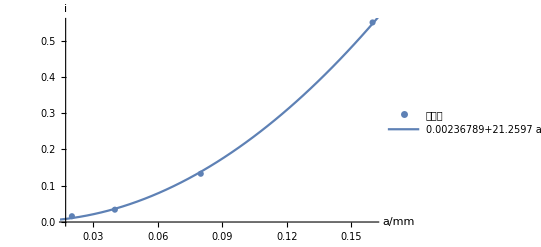

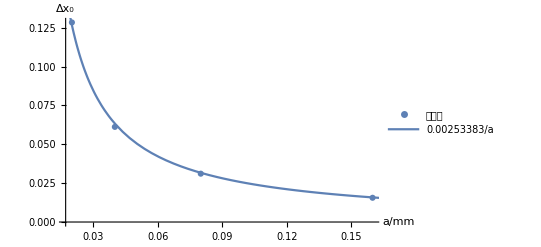

R_1^2→0.999948

```mathematica
Clear[A,B,c]
a={0.02,0.04,0.08,0.16};
i={0.016,0.034,0.133,0.55};
sol1=NMinimize[Total@Table[(i[[n]]-A a[[n]]^2-B)^4,{n,1,Length@a}],{A,B},Method->"SimulatedAnnealing"];
sol2=NMinimize[Total@Table[(Subscript[Δx, 0][[n]]-c/a[[n]])^4,{n,1,Length@a}],{c},Method->"SimulatedAnnealing",WorkingPrecision->MachinePrecision];
A=A/.sol1[[2]];B=B/.sol1[[2]];c=c/.sol2[[2]];
Show[ListPlot[Transpose@{a,i},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"a/mm","i"},PlotRange->All,PlotLegends->{实验值}],Plot[A α^2+B,{α,0,0.165},PlotLegends->{A "a^2"+B},ImageSize->400]]
Show[ListPlot[Transpose@{a,Subscript[Δx, 0]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"a/mm","Δx_0"},PlotRange->All,PlotLegends->{实验值}],Plot[c/α,{α,0,0.165},PlotLegends->{c/ "a"},ImageSize->400]]
Subscript[R, 1]^2->1-Sum[(i[[n]]-A (a^2)[[n]]-B)^2,{n,1,Length@a}]/Sum[(i[[n]]-Total@i/Length@i)^2,{n,1,Length@a}]
Subscript[R, 2]^2->1-Sum[(Subscript[Δx, 0][[n]]-c/a[[n]])^2,{n,1,Length@a}]/Sum[(Subscript[Δx, 0][[n]]-Total@Subscript[Δx, 0]/Length@Subscript[Δx, 0])^2,{n,1,Length@a}]
```

```mathematica
(*多缝*)
```

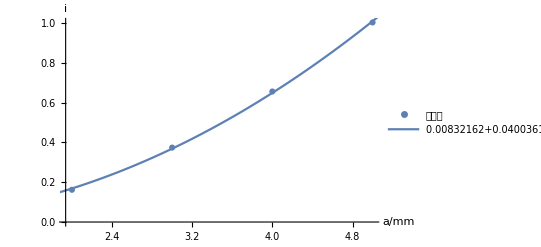

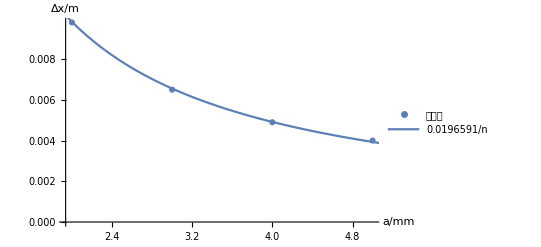

R_1^2→0.999986

R_2^2→0.999994

```mathematica
Clear[n,F,G,H,J]
n={2,3,4,5};
Subscript[i, 2]={0.162,0.374,0.656,1.003};
Subscript[Δx, 2]={0.0098,0.0065,0.0049,0.004};
sol3=NMinimize[Total@Table[(Subscript[i, 2][[j]]-F n[[j]]^2-G)^4,{j,1,Length@n}],{F,G},Method->"SimulatedAnnealing"];
F=F/.sol3[[2]];G=G/.sol3[[2]];
sol4=NMinimize[Total@Table[(Subscript[Δx, 2][[j]]-H/n[[j]])^4,{j,1,Length@n}],{H},Method->"SimulatedAnnealing"];
H=H/.sol4[[2]];
Show[ListPlot[Transpose@{n,Subscript[i, 2]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"a/mm","i"},PlotRange->All,PlotLegends->{实验值}],Plot[F α^2+G,{α,1.5,5.5},PlotLegends->{F "n^2"+G},ImageSize->400]]
Show[ListPlot[Transpose@{n,Subscript[Δx, 2]},ImageSize->400,PlotMarkers->Automatic,AxesLabel->{"a/mm","Δx/m"},PlotRange->All,PlotLegends->{实验值}],Plot[H/α,{α,1.5,5.5},PlotLegends->{H/"n"},ImageSize->400]]
Subscript[R, 1]^2->1-Sum[(Subscript[i, 2][[j]]-F n[[j]]^2-G)^2,{j,1,Length@n}]/Sum[(Subscript[i, 2][[j]]-Total@Subscript[i, 2]/Length@Subscript[i, 2])^2,{j,1,Length@n}]
Subscript[R, 2]^2->1-Sum[(Subscript[Δx, 2][[j]]-H/n[[j]])^2,{j,1,Length@n}]/Sum[(Subscript[Δx, 2][[j]]-Total@Subscript[Δx, 2]/Length@Subscript[Δx, 2])^2,{j,1,Length@n}]
```

```mathematica
整流电路
```

```mathematica
i=Subscript[I, s](ⅇ^(u/Subscript[U, T])-1) ⟹ Si:i>>0,u≈0.7V      u<0 ⟹ i=0
Subscript[R, L]=1000Ω ,C=100μF
Subscript[V, max]/V
```

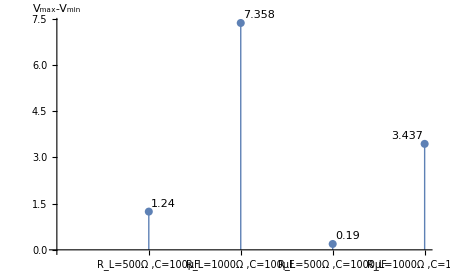

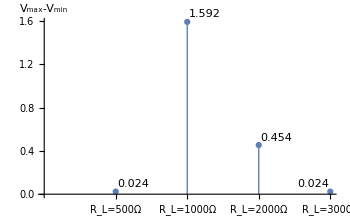

```mathematica
expr1={"R_L=500Ω ,C=100μF","R_L=1000Ω ,C=100μF","R_L=500Ω ,C=1000μF","R_L=1000Ω ,C=1000μF"};
expr2={"R_L=500Ω" ,"R_L=1000Ω" ,"R_L=2000Ω" ,"R_L=3000Ω" };
max1={8.447,7.856,8.281,7.524};
min1={7.207,0.498,8.091,4.087};
max2={4.98,4.888,4.932,4.946};
min2={4.956,3.296,4.478,4.922};
ListPlot[Labeled[#,#]&/@(max1-min1),Filling->Bottom,AxesLabel->{,Subscript[V, max]-Subscript[V, min]},FillingStyle->{Blue,Thick},Ticks->{Transpose@{{1,2,3,4},expr1},Automatic},TicksStyle->Directive["Label", 8.2],ImageSize->450]
ListPlot[Labeled[#,#]&/@(max2-min2),Filling->Bottom,AxesLabel->{,Subscript[V, max]-Subscript[V, min]},FillingStyle->{Blue,Thick},Ticks->{Transpose@{{1,2,3,4},expr2},Automatic},ImageSize->350]
```

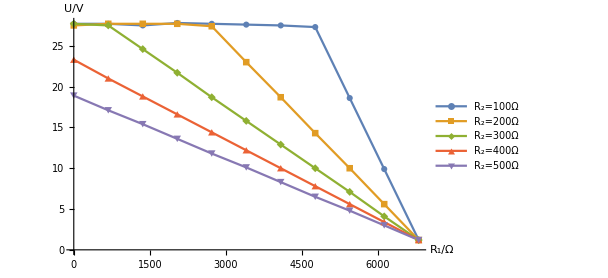

```mathematica
R={0,680,1360,2040,2720,3400,4080,4760,5440,6120,6800};
Subscript[U, 100]={27.7,27.7,27.5,27.8,27.7,27.6,27.5,27.3,18.6,9.9,1.2};
Subscript[U, 200]={27.5,27.7,27.7,27.7,27.4,23,18.7,14.3,10,5.6,1.2};
Subscript[U, 300]={27.7,27.5,24.6,21.7,18.7,15.8,12.9,10,7.1,4.1,1.2};
Subscript[U, 400]={23.3,21,18.8,16.6,14.4,12.2,10,7.8,5.6,3.4,1.2};
Subscript[U, 500]={18.9,17.1,15.4,13.6,11.8,10.1,8.3,6.5,4.8,3,1.2};
ListLinePlot[Table[Transpose@{R,Subscript[U, i]},{i,100,500,100}],ImageSize->450,PlotMarkers->Automatic,AxesLabel->{"R_1/Ω","U/V"},PlotRange->All,PlotLegends->{"R_2=100Ω","R_2=200Ω","R_2=300Ω","R_2=400Ω","R_2=500Ω"},PlotStyle->Thin]
```

```mathematica
温度传感器
```

```mathematica
Subscript[R, T]=Subscript[R, 0] e^(B(1/T-1/Subscript[T, 0]))       Subscript[R, T]=a/T+c
 Subscript[U, F]=Subscript[U, g]+Subscript[k, B]/q(Ln Subscript[I, F]/B-(3+r/2)Ln T)T       Subscript[R, F]=Subscript[U, F]/Subscript[I, F]≈((Ln i/B Subscript[k, B])/(i q)+Subscript[U, g])+((-3-r/2+Ln i/B) Subscript[k, B] (T-1))/(i q)≈b T+d
```

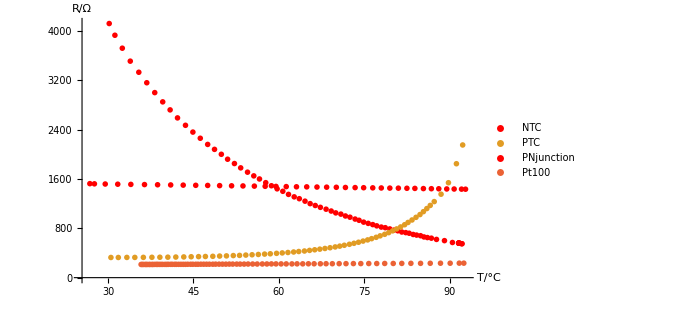

```mathematica
ListPlot[{Table[(Transpose@{Subscript[T, NTC],Subscript[R, NTC]})[[i]],{i,1,Length@Subscript[T, NTC],50}],Table[(Transpose@{Subscript[T, PTC],Subscript[R, PTC]})[[i]],{i,1,Length@Subscript[T, PTC],50}],Table[(Transpose@{Subscript[T, PNJ],Subscript[R, PNJ]})[[i]],{i,1,Length@Subscript[T, PNJ],50}],Table[(Transpose@{Subscript[T, Pt100],Subscript[R, Pt100]})[[i]],{i,1,Length@Subscript[T, Pt100],50}]},ImageSize->500,AxesLabel->{"T/°C","R/Ω"},PlotRange->All,PlotLegends->{NTC,PTC,PNjunction,Pt100},PlotStyle->{Red,PointSize[10^-2]},PlotMarkers->"OpenMarkers"]
```

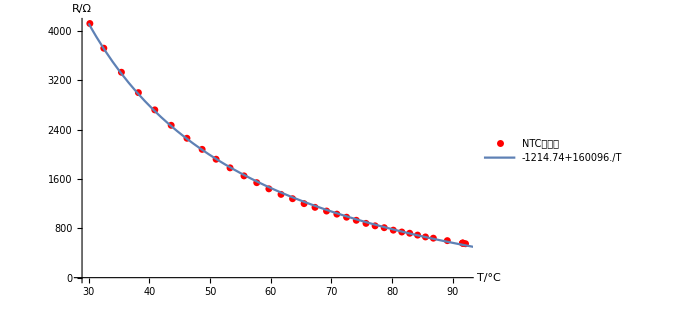

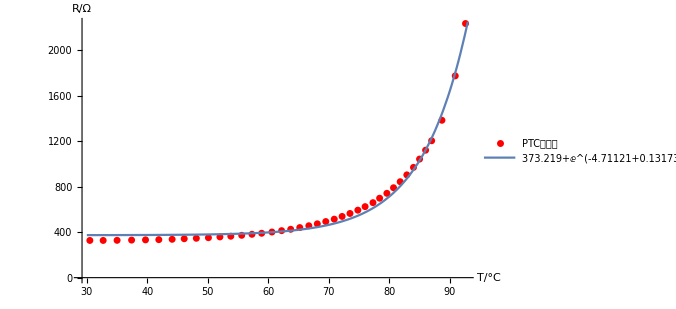

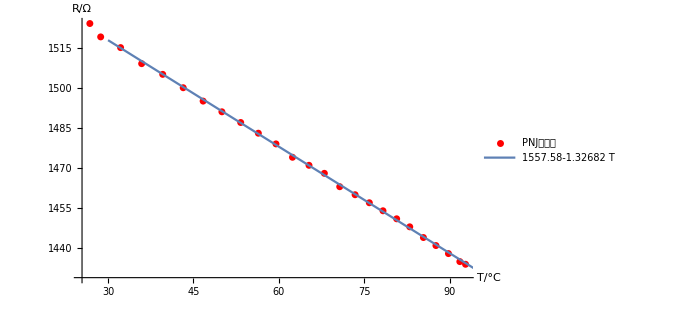

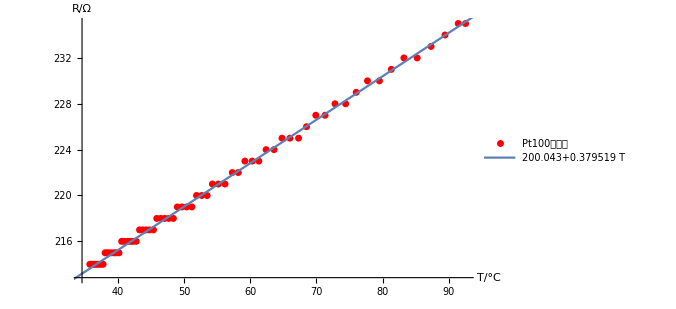

```mathematica
Clear["Global`*"]
Subscript[i, NTC]=1*10^-4;Subscript[i, PTC]=1*10^-3;Subscript[i, PNJ]=1*10^-3;Subscript[i, Pt100]=1*10^-3;
Subscript[T, NTC]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor(NTC).xlsx")[[1]])[[2]];
Subscript[U, NTC]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor(NTC).xlsx")[[1]])[[3]];
Subscript[T, PTC]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor(PTC).xlsx")[[1]])[[2]];
Subscript[U, PTC]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor(PTC).xlsx")[[1]])[[3]];
Subscript[T, PNJ]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor-PN_junction.xlsx")[[1]])[[2]];
Subscript[U, PNJ]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor-PN_junction.xlsx")[[1]])[[3]];
Subscript[T, Pt100]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor-Pt100.xlsx")[[1]])[[2]];
Subscript[U, Pt100]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor-Pt100.xlsx")[[1]])[[3]];

Subscript[R, NTC]=Subscript[U, NTC]/Subscript[i, NTC];Subscript[R, PTC]=Subscript[U, PTC]/Subscript[i, PTC];Subscript[R, PNJ]=Subscript[U, PNJ]/Subscript[i, PNJ];Subscript[R, Pt100]=Subscript[U, Pt100]/Subscript[i, Pt100];
sol1=NMinimize[Total@Table[(Subscript[R, NTC][[j]]-a/Subscript[T, NTC][[j]]-r)^4,{j,1,Length@Subscript[R, NTC]}],{a,r},Method->"SimulatedAnnealing"];
sol2=NMinimize[Total@Table[(Subscript[R, PTC][[j]]-Exp[b Subscript[T, PTC][[j]]+b2]-r2)^6,{j,1,Length@Subscript[R, PTC]}],{b,b2,r2},Method->"SimulatedAnnealing"];
sol3=NMinimize[Total@Table[(Subscript[R, PNJ][[j]]-c Subscript[T, PNJ][[j]]-r3)^4,{j,1,Length@Subscript[R, PNJ]}],{c,r3},Method->"SimulatedAnnealing"];
sol4=NMinimize[Total@Table[(Subscript[R, Pt100][[j]]-d Subscript[T, Pt100][[j]]-r4)^4,{j,1,Length@Subscript[R, Pt100]}],{d,r4},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];r=r/.sol1[[2]];
b=b/.sol2[[2]];b2=b2/.sol2[[2]];r2=r2/.sol2[[2]];c=c/.sol3[[2]];
r3=r3/.sol3[[2]];d=d/.sol4[[2]];r4=r4/.sol4[[2]];
Show[ListPlot[Table[(Transpose@{Subscript[T, NTC],Subscript[R, NTC]})[[i]],{i,1,Length@Subscript[T, NTC],100}],ImageSize->500,AxesLabel->{"T/°C","R/Ω"},PlotRange->All,PlotLegends->{NTC实验值},PlotStyle->{Red,PointSize[10^-2]}],Plot[a/T+r,{T,30,95},PlotLegends->{a/T+r}]]
Show[ListPlot[Table[(Transpose@{Subscript[T, PTC],Subscript[R, PTC]})[[i]],{i,1,Length@Subscript[T, PTC],80}],ImageSize->500,AxesLabel->{"T/°C","R/Ω"},PlotRange->All,PlotLegends->{PTC实验值},PlotStyle->{Red,PointSize[10^-2]}],Plot[Exp[b T+b2]+r2,{T,30,98},PlotLegends->{Exp[b T+b2]+r2}]]
Show[ListPlot[Table[(Transpose@{Subscript[T, PNJ],Subscript[R, PNJ]})[[i]],{i,1,Length@Subscript[T, PNJ],80}],ImageSize->500,AxesLabel->{"T/°C","R/Ω"},PlotRange->All,PlotLegends->{PNJ实验值},PlotStyle->{Red,PointSize[10^-2]}],Plot[c T+r3,{T,30,95},PlotLegends->{c T+r3}]]
Show[ListPlot[Table[(Transpose@{Subscript[T, Pt100],Subscript[R, Pt100]})[[i]],{i,1,Length@Subscript[T, Pt100],60}],ImageSize->500,AxesLabel->{"T/°C","R/Ω"},PlotRange->All,PlotLegends->{Pt100实验值},PlotStyle->{Red,PointSize[10^-2]}],Plot[d T+r4,{T,30,95},PlotLegends->{d T+r4}]]
```

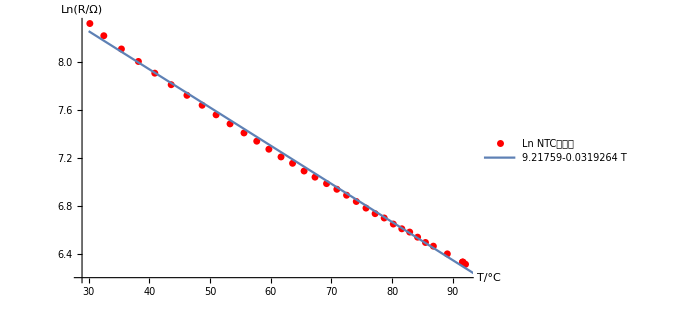

```mathematica
Clear["Global`*"]
Subscript[i, NTC]=1*10^-4;Subscript[i, PTC]=1*10^-3;Subscript[i, PNJ]=1*10^-3;Subscript[i, Pt100]=1*10^-3;
Subscript[T, NTC]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor(NTC).xlsx")[[1]])[[2]];
Subscript[U, NTC]=(Transpose@(Import@"C:\\Users\\Numerical Lab2\\Documents\\大学物理实验3\\T_sensor(NTC).xlsx")[[1]])[[3]];

Subscript[R, NTC]=Subscript[U, NTC]/Subscript[i, NTC];Subscript[R, PTC]=Subscript[U, PTC]/Subscript[i, PTC];Subscript[R, PNJ]=Subscript[U, PNJ]/Subscript[i, PNJ];Subscript[R, Pt100]=Subscript[U, Pt100]/Subscript[i, Pt100];Subscript[lnR, NTC]=Log[Subscript[R, NTC]];
sol1=NMinimize[Total@Table[(Subscript[lnR, NTC][[j]]-a Subscript[T, NTC][[j]]-r)^4,{j,1,Length@Subscript[lnR, NTC]}],{a,r},Method->"SimulatedAnnealing"];
a=a/.sol1[[2]];r=r/.sol1[[2]];
Show[ListPlot[Table[(Transpose@{Subscript[T, NTC],Subscript[lnR, NTC]})[[i]],{i,1,Length@Subscript[T, NTC],100}],ImageSize->500,AxesLabel->{"T/°C","Ln(R/Ω)"},PlotRange->All,PlotLegends->{Ln(NTC实验值)},PlotStyle->{Red,PointSize[10^-2]}],Plot[a T+r,{T,30,95},PlotLegends->{a T+r}]]
```

```mathematica
Subscript[(R^2), NTC]-> 1-Sum[(Subscript[R, NTC][[j]]-a/Subscript[T, NTC][[j]]-r)^2,{j,1,Length@Subscript[R, NTC]}]/Sum[(Subscript[R, NTC][[j]]-Total@Subscript[R, NTC]/Length@Subscript[R, NTC])^2,{j,1,Length@Subscript[R, NTC]}]
Subscript[(R^2), PTC]-> 1-Sum[(Subscript[R, PTC][[j]]-Exp[b Subscript[T, PTC][[j]]+b2]-r2)^2,{j,1,Length@Subscript[R, PTC]}]/Sum[(Subscript[R, PTC][[j]]-Total@Subscript[R, PTC]/Length@Subscript[R, PTC])^2,{j,1,Length@Subscript[R, PTC]}]
Subscript[(R^2), PNJ]-> 1-Sum[(Subscript[R, PNJ][[j]]-c Subscript[T, PNJ][[j]]-r3)^2,{j,1,Length@Subscript[R, PNJ]}]/Sum[(Subscript[R, PNJ][[j]]-Total@Subscript[R, PNJ]/Length@Subscript[R, PNJ])^2,{j,1,Length@Subscript[R, PNJ]}]
Subscript[(R^2), Pt100]-> 1-Sum[(Subscript[R, Pt100][[j]]-d Subscript[T, Pt100][[j]]-r4)^2,{j,1,Length@Subscript[R, Pt100]}]/Sum[(Subscript[R, Pt100][[j]]-Total@Subscript[R, Pt100]/Length@Subscript[R, Pt100])^2,{j,1,Length@Subscript[R, Pt100]}]
```

(R^2)_NTC→0.999605

(R^2)_PTC→0.991616

(R^2)_PNJ→0.999604

(R^2)_Pt100→0.997594

```mathematica
Subscript[RT, Pt100]=Transpose@{Subscript[T, Pt100],Subscript[R, Pt100]};
tab=Table[(Subscript[RT, Pt100][[T+1]]-Subscript[RT, Pt100][[T]])[[1]],{T,1,Length@Subscript[RT, Pt100]-1}]
Subscript[R, Pt100][[Position[tab,-0.10000000000000142]//Flatten]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,-0.1,0.,0.,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,-0.1,0.,0.,0.,0.,-0.1,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.}

{224.,224.,224.,224.,224.,224.,224.,224.,224.,224.,224.,224.,224.,224.,224.,224.,224.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,223.,222.,223.,222.,222.,222.,222.,222.,222.,222.,222.,222.,222.,222.,222.,222.,222.,222.,222.,222.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,221.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,220.,219.,220.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,219.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,218.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,217.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,216.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,215.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.,214.}

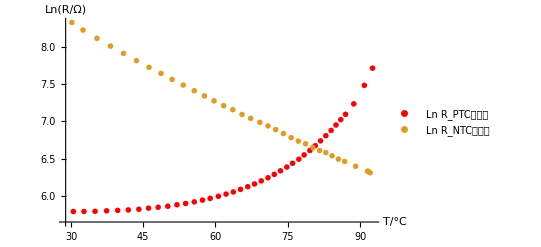

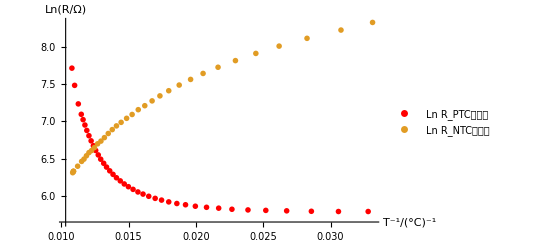

```mathematica
ListPlot[{Table[(Transpose@{Subscript[T, PTC],Subscript[LnR, PTC]})[[i]],{i,1,Length@Subscript[T, PTC],80}],Table[(Transpose@{Subscript[T, NTC],Subscript[lnR, NTC]})[[i]],{i,1,Length@Subscript[T, NTC],100}]},ImageSize->400,AxesLabel->{"T/°C","Ln(R/Ω)"},PlotRange->All,PlotLegends->{"Ln R_PTC实验值","Ln R_NTC实验值"},PlotStyle->{Red,PointSize[10^-2]},PlotMarkers->"OpenMarkers"]
ListPlot[{Table[(Transpose@{1/Subscript[T, PTC],Subscript[LnR, PTC]})[[i]],{i,1,Length@Subscript[T, PTC],80}],Table[(Transpose@{1/Subscript[T, NTC],Subscript[lnR, NTC]})[[i]],{i,1,Length@Subscript[T, NTC],100}]},ImageSize->400,AxesLabel->{"T^-1/(°C)^-1","Ln(R/Ω)"},PlotRange->All,PlotLegends->{"Ln R_PTC实验值","Ln R_NTC实验值"},PlotStyle->{Red,PointSize[10^-2]},PlotMarkers->"OpenMarkers"]
```

```mathematica
Clear["Global`*"]
```